## Simulation pipeline

#### a. upstream

We assume upstream has a linear network, which generates a oscillated MAP2K with concentration of A(1+mag*Sin[2π (f t+phase)])

#### b. p38

We use Forth Order Runge-Kutta Method consider the high nonlinearity of p38’s rate equations
ref: https://en.wikipedia.org/wiki/Runge–Kutta_methods

```mathematica
p38RKsolve[A0_,B0_,C0_,dt_,T_,funcs_]:=Module[
{A=A0,B=B0,C=C0,solA,solB,solC,t=0.,i=1,k11,k12,k13,k21,k22,k23,k31,k32,k33,k41,k42,k43},
solA={{t,A0}};
solB={{t,B0}};
solC={{t,C0}};
While[t<T-10^-6,
{k11,k12,k13}=Table[f[t,A,B,C],{f,funcs}];
{k21,k22,k23}=Table[f[t+dt/2,A+dt/2 k11,B+dt/2 k12,C+dt/2 k13],{f,funcs}];
{k31,k32,k33}=Table[f[t+dt/2,A+dt/2 k21,B+dt/2 k22,C+dt/2 k23],{f,funcs}];
{k41,k42,k43}=Table[f[t+dt,A+dt k31,B+dt k32,C+dt k33],{f,funcs}];
{A,B,C}={A,B,C}+dt/6({k11,k12, k13}+2{k21,k22, k23}+2{k31,k32, k33}+{k41,k42, k43});
A=Max[A,0.];
B=Max[B,0.];
C=Max[C,0.];
t+=dt;
AppendTo[solA,{t,A}];
AppendTo[solB,{t,B}];
AppendTo[solC,{t,C}];
i+=1];
(*return values*)
{solA,solB,solC}];
```

Solver for p38
Note: Rate constants are in units of hr^-1. Total Time (totT) and dt have units of hour.

```mathematica
p38solve[initA_,initB_,initC_,driveA_,mag_,f_,phase_,totT_:140]:=Module[{funcs,dt=0.001,fac=6.5,plotrange},
(*-----Rate equations for p38, with a drive: A(1+mag Sin[2π(ft+phase)])-----------*)
funcs={Function[{t,A,B,C},k2*driveA(1.+ mag Sin[2π (f t+phase)])*(1-A)-k3*(A*C)/(k4+A)],
             Function[{t,A,B,C},k5*A*(1-B)-k6*B],
             Function[{t,A,B,C},k7*B*(1-C)-k8*C]}//.{k2->(0.15*fac),k3->(0.16*fac),k4->0.0001,k5->(0.055*fac),k6->(0.05*fac),k7->(0.2*fac),k8->(0.02*fac)};
(*--------------------Solve By Runge–Kutta-----------------------*)
p38RKsolve[initA,0.01,0.01,dt,totT,funcs][[1]]];
```

#### c. downstream

```mathematica
downstreamsolver[beta1_,alpha1_,alpha2_,beta2_,initA_,initB_,mag_,drive_]:=
Module[
{NAF,NF,A,B,solA,solB,totT=drive[[-1,1]],dt=drive[[2,1]]-drive[[1,1]],t,i,noise},
NAF=Im[Eigenvalues[{{-beta1,-alpha1},{alpha2,-beta2}}][[1]]];
NF=NAF/2/π;
(*Print["Natural Freq is:", NF," Period T is:",1/(NAF/2/π)];*)
(*------------------------Solve Equation--------------------------*)
A=initA;
B=initB;
t=0.;
i=1;
solA={{t,A}};
solB={{t,B}};
While[t<totT,
A=A+dt*(-beta1 A-alpha1 B+mag*drive[[i,2]]);
B=B+dt*(alpha2 A-beta2 B);
t+=dt;
AppendTo[solA,{t,A}];
AppendTo[solB,{t,B}];
i+=1];
solA]
```

#### Auxiliary functions

Discrete Fourier Transform

```mathematica
fouriertransform[sol_,dtime_]:=Module[
{dt, data,L,freq,FreqPeakPos,FreqPeakandWidth,leftf,rightf,df,NF1,NF2,NF},
dt = sol[[2,1]]-sol[[1,1]];
freq=Flatten[
Table[data=sol[[;;j]][[All,2]];
L=Length[data];
{Table[(n-1)/(dt Length[data]),{n,Length[data]}],Abs[Fourier[data]]}ᵀ,
{j,Ceiling[Length[sol]/2],Length[sol],Ceiling[dtime/dt]}],1];
Select[Sort[freq],#[[1]]<1.&]]
```

Brown Noise Generator follows Wiener process: 
https://en.wikipedia.org/wiki/Wiener_process
which has Gausian increment, i.e. W_(t+dt)-W_t ~ N(0, dt)             (μ=0, σ^2=dt) 
Note: Wiener process is a continuum limit of random walk

```mathematica
brownnoise[totT_,dt_]:=Module[{brownNoise},
brownNoise=Accumulate[RandomVariate[NormalDistribution[0,Sqrt[dt]],Ceiling[totT/dt]]];
brownNoise/Max[Abs[brownNoise]]]
```

```mathematica
addnoise[solA_,noiseA_]:=Module[{noise,newsolA,freq,totT,dt},
totT=solA[[-1,1]];
dt=solA[[2,1]]-solA[[1,1]];
noise=Join[{0},noiseA*brownnoise[totT,dt]];
Table[{solA[[i,1]],solA[[i,2]]+noise[[i]]},{i,1,Length[solA]}]];
```

## Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Upstream f=0.09

Upstream generates a oscillated MAP2K with frequency f = 0.09.
To solve p38, we apply “driveA(1+mag Sin[2π (f t+phase)])” as the drive function,
where driveA=0.2857, mag = rand(),f = 0.09,phase=rand()
p38 can be solved by running the following codes:
                              p38solf009ensemble = Table[p38solve[(*initA*)RandomReal[],(*initB*)RandomReal[],(*initC*)RandomReal[],(*driveA*)0.2857,(*mag*)RandomReal[],(*f*)0.09,(*phase*)RandomReal[]], {i, 1, 100}]
The running is time costly. In the following sections, we will import data from previously solved and saved solution.
The brown noise is added to the solution to compare with the experiments.

```mathematica
savedp38solf009ensemble=Table[
oridata=Import["p38_f_009/data_"<>ToString[i]<>".csv"];
startT=RandomInteger[{30,40}];
{#1-startT,#2}&@@@Select[oridata,(startT+100.001)>#[[1]]>(startT-0.001)&],{i,1,100}];
p38solf009ensembleNoise=Table[addnoise[sol,0.1],{sol,savedp38solf009ensemble}];
p38solf009ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,p38solf009ensembleNoise}];
```

We design two substrates A&B:
substrate A has a Natural Frequency of 0.18hr^-1
substrate B has a Natural Frequency of 0.36hr^-1
The substrate is solved using “downstreamsolver” function, with p38 acting as the driving force.

```mathematica
{beta1,alpha1,alpha2,beta2}={0.004,1.6,0.8,0.004};
subAsolf009ensemble=ParallelTable[downstreamsolver[beta1,alpha1,alpha2,beta2,0.,0.,RandomReal[],sol],{sol,savedp38solf009ensemble}];
subAsolf009ensembleNoise=Table[addnoise[sol,0.1],{sol,subAsolf009ensemble}];
subAsolf009ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,subAsolf009ensembleNoise}];
```

```mathematica
{beta1,alpha1,alpha2,beta2}={0.004,3.2,1.6,0.004};
subBsolf009ensemble=ParallelTable[downstreamsolver[beta1,alpha1,alpha2,beta2,0.,0.,RandomReal[],sol],{sol,savedp38solf009ensemble}];
subBsolf009ensembleNoise=Table[addnoise[sol,0.1],{sol,subBsolf009ensemble}];
subBsolf009ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,subBsolf009ensembleNoise}];
```

### Upstream f=0.36

Upstream generates a oscillated MAP2K with frequency f = 0.36.

```mathematica
savedp38solf036ensemble=Table[
oridata=Import["p38_f_036/data_"<>ToString[i]<>".csv"];
startT=RandomInteger[{30,40}];
{#1-startT,#2}&@@@Select[oridata,(startT+100.001)>#[[1]]>(startT-0.001)&],{i,1,100}];
p38solf036ensembleNoise=Table[addnoise[sol,0.1],{sol,savedp38solf036ensemble}];
p38solf036ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,p38solf036ensembleNoise}];
```

```mathematica
{beta1,alpha1,alpha2,beta2}={0.004,1.6,0.8,0.004};
subAsolf036ensemble=ParallelTable[downstreamsolver[beta1,alpha1,alpha2,beta2,0.,0.,RandomReal[],sol],{sol,savedp38solf036ensemble}];
subAsolf036ensembleNoise=Table[addnoise[sol,0.1],{sol,subAsolf036ensemble}];
subAsolf036ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,subAsolf036ensembleNoise}];
```

```mathematica
{beta1,alpha1,alpha2,beta2}={0.004,3.2,1.6,0.004};
subBsolf036ensemble=ParallelTable[downstreamsolver[beta1,alpha1,alpha2,beta2,0.,0.,RandomReal[],sol],{sol,savedp38solf036ensemble}];
subBsolf036ensembleNoise=Table[addnoise[sol,0.1],{sol,subBsolf036ensemble}];
subBsolf036ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,subBsolf036ensembleNoise}];
```

### Upstream f=0.27

Upstream generates a oscillated MAP2K with frequency f = 0.27.

```mathematica
savedp38solf027ensemble=Table[
oridata=Import["p38_f_027/data_"<>ToString[i]<>".csv"];
startT=RandomInteger[{30,40}];
{#1-startT,#2}&@@@Select[oridata,(startT+100.001)>#[[1]]>(startT-0.001)&],{i,1,100}];;
p38solf027ensembleNoise=Table[addnoise[sol,0.1],{sol,savedp38solf027ensemble}];
p38solf027ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,p38solf027ensembleNoise}];
```

```mathematica
{beta1,alpha1,alpha2,beta2}={0.004,1.6,0.8,0.004};
subAsolf027ensemble=ParallelTable[downstreamsolver[beta1,alpha1,alpha2,beta2,0.,0.,RandomReal[],sol],{sol,savedp38solf027ensemble}];
subAsolf027ensembleNoise=Table[addnoise[sol,0.1],{sol,subAsolf027ensemble}];
subAsolf027ensembleFreq=Table[fouriertransform[sol,0.,1.],{sol,subAsolf027ensembleNoise}];
```

```mathematica
{beta1,alpha1,alpha2,beta2}={0.004,3.2,1.6,0.004};
subBsolf027ensemble=ParallelTable[downstreamsolver[beta1,alpha1,alpha2,beta2,0.,0.,RandomReal[],sol],{sol,savedp38solf027ensemble}];
subBsolf027ensembleNoise=Table[addnoise[sol,0.1],{sol,subBsolf027ensemble}];
subBsolf027ensembleFreq=Table[fouriertransform[sol,40.,1.],{sol,subBsolf027ensembleNoise}];
```

## Ensemble Stories

#### plot function

```mathematica
plotfrequency[p38_,subA_,subB_,plotrange_:{{0,1.},{0,5}}]:=GraphicsColumn[{
Show[Legended[ListLinePlot[{DeleteDuplicatesBy[p38,First]},
Frame->True,FrameTicks->{{{#,TextString[#]}&/@Range[Ceiling[plotrange[[2,2]]/4],plotrange[[2,2]],Ceiling[plotrange[[2,2]]/4]],None},{None,None}},FrameStyle->12,FrameLabel->{None,"A"},
PlotRange->plotrange,PlotStyle->{RGBColor[1, 0.65, 0.15]},Joined->True,AspectRatio->1/2],
Placed[LineLegend[{RGBColor[1, 0.65, 0.15]},{"p38"}],{0.8,0.8}]],
ImageSize->300,ImagePadding->{{80,10},{50,10}}],Show[Legended[ListLinePlot[{DeleteDuplicatesBy[subA,First],DeleteDuplicatesBy[subB,First]},
Frame->True,FrameTicks->{{{#,TextString[#]}&/@Range[0,plotrange[[2,2]],Ceiling[plotrange[[2,2]]/4]],None},{{#,TextString[#]}&/@Range[0,1,0.2],None}},FrameStyle->12,FrameLabel->{"Frequency (hrs^-1)","A"},
PlotRange->plotrange,PlotStyle->{RGBColor[0.33, 0.59, 0.47000000000000003],RGBColor[0.33, 0.59, 1]},Joined->True,AspectRatio->1/2],
Placed[LineLegend[{RGBColor[0.33, 0.59, 0.47000000000000003],RGBColor[0.33, 0.59, 1]},{"Substrate A", "Substrate B"}],{0.78,0.75}]],
ImageSize->300,ImagePadding->{{80,10},{50,10}}]},
Spacings->{0,{0,-54}}]
```

```mathematica
plotsolution[p38_,subA_,subB_,plotrange_:{{0,100},{-0.4,0.4}}]:=Module[{p38mean,subAmean,subBmean},
p38mean=Mean[p38];
subAmean=Mean[subA];
subBmean=Mean[subB];
GraphicsColumn[{
Show[{ListLinePlot[p38,PlotRange->plotrange,PlotStyle->Directive[RGBColor[1, 0.65, 0.15],Opacity[0.3]],
Frame->True,FrameTicks->{{{#,TextString[#]}&/@{-plotrange[[2,2]]/2,0.,plotrange[[2,2]]/2},None},{None,None}},FrameStyle->12,FrameLabel->{None,"p38"},
Joined->True,AspectRatio->1/2],ListLinePlot[p38mean,PlotRange->plotrange,PlotStyle->Directive[RGBColor[1, 0.65, 0.15],Opacity[1.]]]},
ImageSize->350,ImagePadding->{{80,10},{50,10}}],
Show[{ListLinePlot[subA,PlotRange->plotrange,PlotStyle->Directive[RGBColor[0.33, 0.59, 0.47000000000000003],Opacity[0.3]],
Frame->True,FrameTicks->{{{#,TextString[#]}&/@{-plotrange[[2,2]]/2,0.,plotrange[[2,2]]/2},None},{None,None}},FrameStyle->12,FrameLabel->{None,"Substrate A"},Joined->True,AspectRatio->1/2],ListLinePlot[subAmean,PlotRange->plotrange,PlotStyle->Directive[RGBColor[0.33, 0.59, 0.47000000000000003],Opacity[1.]]]},
ImageSize->350,ImagePadding->{{80,10},{50,10}}],
Show[{ListLinePlot[subB,PlotRange->plotrange,PlotStyle->Directive[RGBColor[0.33, 0.59, 1],Opacity[0.2]],
Frame->True,FrameTicks->{{{#,TextString[#]}&/@{-plotrange[[2,2]]/2,0.,plotrange[[2,2]]/2},None},{{#,TextString[#]}&/@Range[0,plotrange[[1,2]],20],None}},FrameStyle->12,FrameLabel->{"Time(hrs)","Substrate B"},Joined->True,AspectRatio->1/2],ListLinePlot[subBmean,PlotRange->plotrange,PlotStyle->Directive[RGBColor[0.33, 0.59, 1],Opacity[1.]]]},
ImageSize->350,ImagePadding->{{80,10},{50,10}}]},
Spacings->{0,{0,-62,-62}}]]
```

#### ensemble

We divide our 100 simulation data into 14 groups, where each group has 7-8 data.

```mathematica
groupids={{1,2,3,4,5,6,7},{8,9,10,11,12,13,14},{15,16,17,18,19,20,21},{22,23,24,25,26,27,28},{29,30,31,32,33,34,35},{36,37,38,39,40,41,42},{43,44,45,46,47,48,49},{50,51,52,53,54,55,56},{57,58,59,60,61,62,63},{64,65,66,67,68,69,70},{71,72,73,74,75,76,77},{78,79,80,81,82,83,84},{85,86,87,88,89,90,91,92},{93,94,95,96,97,98,99,100}};
```

The following frequency plots show the ensemble average of the 14 groups, and the solution plots show the solution and average of the first group we put in the paper.

### Story 1 (On resonance with Substrate A, upstream f=0.09)

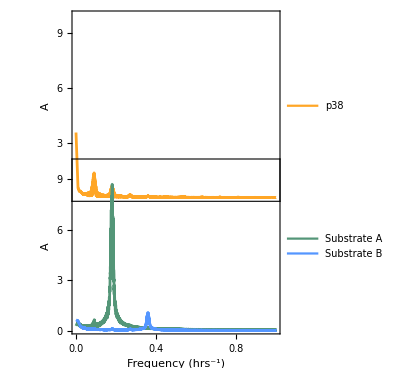

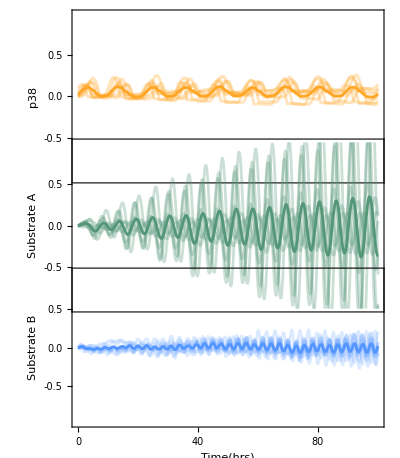

```mathematica
plotfrequency[Mean[Table[fouriertransform[Mean[p38solf009ensembleNoise[[groupid]]],1.],{groupid,groupids}]],
Mean[Table[fouriertransform[Mean[subAsolf009ensembleNoise[[groupid]]],1.],{groupid,groupids}]],
Mean[Table[fouriertransform[Mean[subBsolf009ensembleNoise[[groupid]]],1.],{groupid,groupids}]],{{0,1.},{0,10}}]
plotsolution[p38solf009ensembleNoise[[groupids[[1]],;;;;10]],subAsolf009ensembleNoise[[groupids[[1]],;;;;10]],subBsolf009ensembleNoise[[groupids[[1]],;;;;10]],{{0,100},{-1.,1.}}]
```

### Story 2 (On resonance with Substrate B, upstream f=0.36)

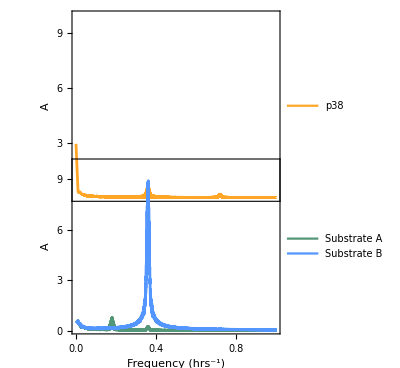

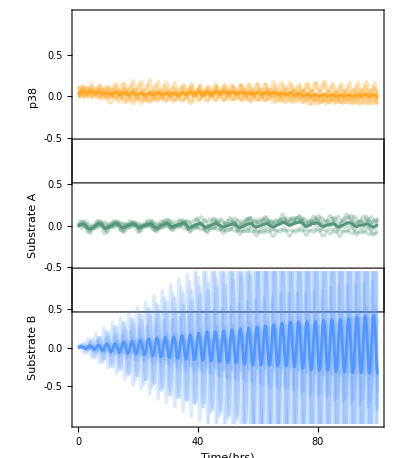

```mathematica
plotfrequency[Mean[Table[fouriertransform[Mean[p38solf036ensembleNoise[[groupid]]],1.],{groupid,groupids}]],
Mean[Table[fouriertransform[Mean[subAsolf036ensembleNoise[[groupid]]],1.],{groupid,groupids}]],
Mean[Table[fouriertransform[Mean[subBsolf036ensembleNoise[[groupid]]],1.],{groupid,groupids}]],{{0,1.},{0,10}}]
plotsolution[p38solf036ensembleNoise[[groupids[[1]],;;;;10]],subAsolf036ensembleNoise[[groupids[[1]],;;;;10]],subBsolf036ensembleNoise[[groupids[[1]],;;;;10]],{{0,100},{-1.,1.}}]
```

### Story 3 (Off resonance with Both Substrates, upstream f=0.27)

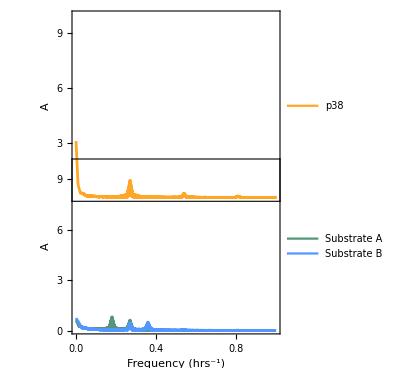

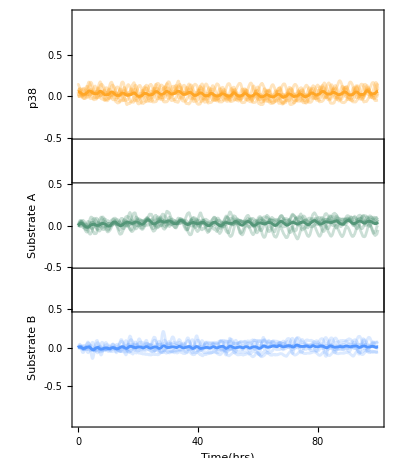

```mathematica
plotfrequency[Mean[Table[fouriertransform[Mean[p38solf027ensembleNoise[[groupid]]],1.],{groupid,groupids}]],
Mean[Table[fouriertransform[Mean[subAsolf027ensembleNoise[[groupid]]],1.],{groupid,groupids}]],
Mean[Table[fouriertransform[Mean[subBsolf027ensembleNoise[[groupid]]],1.],{groupid,groupids}]],{{0,1.},{0,10}}]
plotsolution[p38solf027ensembleNoise[[groupids[[1]],;;;;10]],subAsolf027ensembleNoise[[groupids[[1]],;;;;10]],subBsolf027ensembleNoise[[groupids[[1]],;;;;10]],{{0,100},{-1.,1.}}]
```